### Problems 1(a) and 1(b)

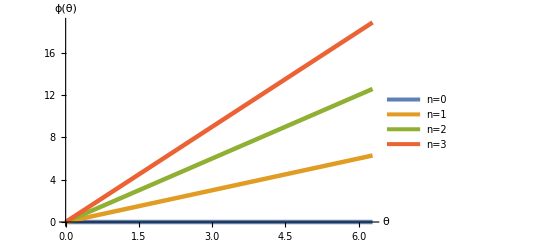

```mathematica
ϕ1[n_]= n*θ;
Plot[{ϕ1[0],ϕ1[1], ϕ1[2], ϕ1[3]},{θ, 0, 2*π}, PlotLegends->{"n=0","n=1","n=2","n=3"}, PlotStyle->Thickness[0.008], AxesLabel->{"θ","ϕ(θ)"}]
```

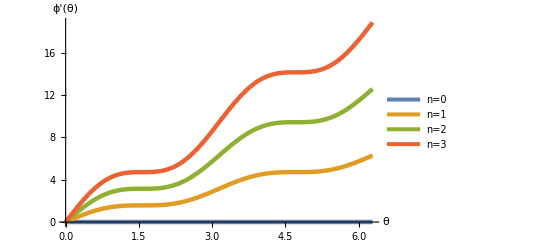

```mathematica
ϕ2[n_]= n*(θ+Cos[θ]*Sin[θ]);
Plot[{ϕ2[0],ϕ2[1], ϕ2[2], ϕ2[3]},{θ, 0, 2*π}, PlotLegends->{"n=0","n=1","n=2","n=3"}, PlotStyle->Thickness[0.008], AxesLabel->{"θ","ϕ'(θ)"}]
```

### Problems 3(a) and 3(b)

```mathematica
num = 10;
size = (num*2 + 1);
TruncHamil = IdentityMatrix[size];
For[i=-num,i<num,i++,{TruncHamil[[i+num+1,i+num+2]]=-eJ/2}]
For[i=-num+1,i<num+1,i++,{TruncHamil[[i+num+1,i+num]]=-eJ/2}]
For[i=-num,i<num+1,i++,{TruncHamil[[i+num+1,i+num+1]]=4*eC*((i)-ng)^2}]
Hamil[ng_,eC_,eJ_] = TruncHamil;
MatrixForm[Hamil[ng,eC,eJ]]
```

(4 eC (-10-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-eJ/2 | 4 eC (-9-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -eJ/2 | 4 eC (-8-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -eJ/2 | 4 eC (-7-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -eJ/2 | 4 eC (-6-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -eJ/2 | 4 eC (-5-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (-4-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (-3-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (-2-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (-1-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC ng^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (1-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (2-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (3-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (4-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (5-ng)^2 | -eJ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (6-ng)^2 | -eJ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (7-ng)^2 | -eJ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (8-ng)^2 | -eJ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (9-ng)^2 | -eJ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -eJ/2 | 4 eC (10-ng)^2)

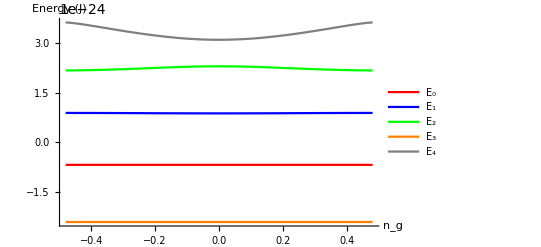

```mathematica
h = 6.63*10^-34;eC= 0.2*10^9*h;eJ= 5*10^9*h;
Plot[{Eigenvalues[Hamil[ng,eC,eJ]][[{size}]],Eigenvalues[Hamil[ng,eC,eJ]][[{size-1}]],Eigenvalues[Hamil[ng,eC,eJ]][[{size-2}]],Eigenvalues[Hamil[ng,eC,eJ]][[{size-3}]],Eigenvalues[Hamil[ng,eC,eJ]][[{size-4}]]},{ng,-0.48,0.48}, PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Orange,Thick},{Gray,Thick}},PlotStyle->Thick,AxesLabel->{"n_g","Energy (J)"},PlotLegends->{"E_0","E_1","E_2","E_3","E_4"},PlotRange-> Full]
```

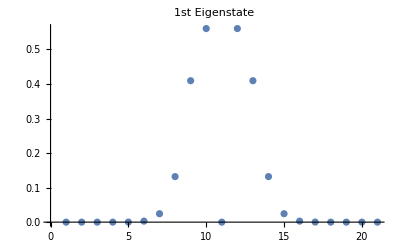

```mathematica
Show[ListPlot[(Abs[Eigenvectors[Hamil[0,eC,eJ]][[{size}]]])], PlotLabel-> "1st Eigenstate"]
```

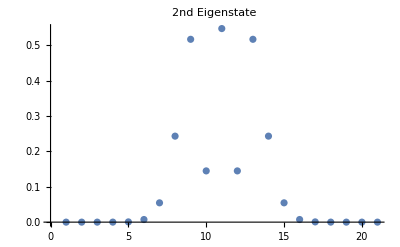

```mathematica
Show[ListPlot[(Abs[Eigenvectors[Hamil[0,eC,eJ]][[{size-1}]]])], PlotLabel-> "2nd Eigenstate"]
```

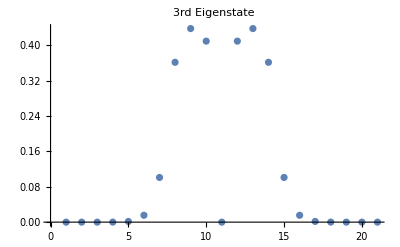

```mathematica
Show[ListPlot[(Abs[Eigenvectors[Hamil[0,eC,eJ]][[{size-2}]]])], PlotLabel-> "3rd Eigenstate"]
```

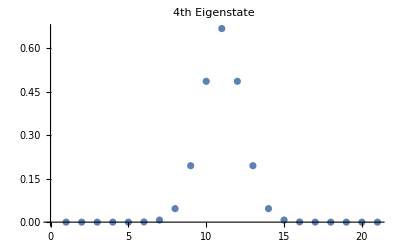

```mathematica
Show[ListPlot[(Abs[Eigenvectors[Hamil[0,eC,eJ]][[{size-3}]]])], PlotLabel-> "4th Eigenstate"]
```

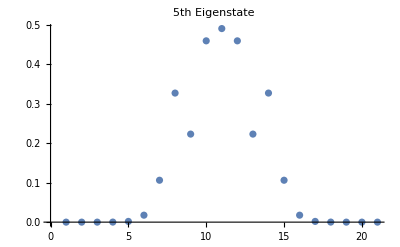

```mathematica
Show[ListPlot[(Abs[Eigenvectors[Hamil[0,eC,eJ]][[{size-4}]]])], PlotLabel-> "5th Eigenstate"]
```